# Sound Speed

## Using Mass Profiles

## Γ = 1 and K = 1

```mathematica
(*This case is somewhat arbitrary. Since the density equation is equal to the pressure equation when Γ and K are equal to 1*)
```

```mathematica
Clear[r]
```

```mathematica
mp1=NDSolveValue[{-16 π^2 m'[r] (6 (3 m[r]+r (-1+m'[r])) m'[r]+r (3 r+r^3 Λ-6 m[r]) m''[r])==0/.Λ->10^-52,m[0.001]==10^-5,m[9000]==0.1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

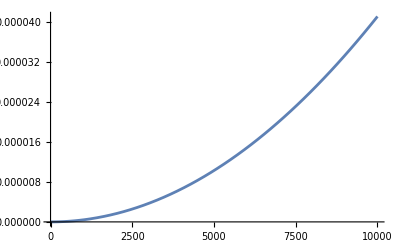

```mathematica
Plot[mp1[r],{r,0.001,10000}]
```

## Γ = 1 and K = r

### Finding dρ/dr

```mathematica
(*We took the mass profile equation for Γ = 1 and K = r. Then made it into the equation for pressure.*)
```

```mathematica
mp2=NDSolveValue[{(-16 π^2 m'[r] ((r^2 (-3+r Λ)+(3+9 r) m[r]) m'[r]+3 r^2 (1+r) m'[r]^2+r^2 (3 r+r^3 Λ-6 m[r]) m''[r]))==0/.{Λ->10^-52},m[0.001]==10^-5,m[9000]==1},m',{r,0.0001,9000}]
```

InterpolatingFunction[…]

```mathematica
(*Below I take the stored mass profile and turn it into a density profile. Then I differentiate the density profile to get dρ/dr for the sound speed equation*)
```

```mathematica
D[mp2[r]/(4 π r^2),r]
```

-(InterpolatingFunction[…][r])/(2 π r^3)+(InterpolatingFunction[…][r])/(4 π r^2)

### Finding dp/dr

```mathematica
(*We took the density profile from the last subsection and put it into our EOS with our assumed values to find dp/dr*)
```

```mathematica
D[(mp2[r]/(4 π r^2))r,r]
```

-(InterpolatingFunction[…][r])/(4 π r^2)+(InterpolatingFunction[…][r])/(4 π r)

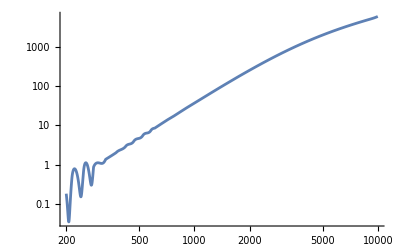

```mathematica
LogLogPlot[(-1/(4 π r^2)InterpolatingFunction[…][r]+1/(4 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r]),{r,200,10000}]
```

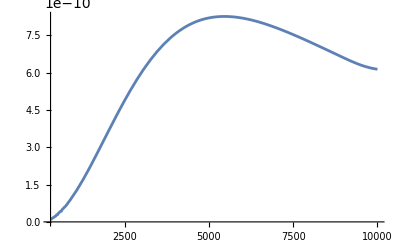

```mathematica
Plot[(mp2[r]/(4 π r^2))((-1/(4 π r^2)InterpolatingFunction[…][r]+1/(4 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r])),{r,300,10000}]
```

## Γ = 1 and K = r/b

```mathematica
(*We took the stored mass profile for the assumed values for Γ and K from the MassGammaKPlots notebook*)
```

```mathematica
mp3=NDSolveValue[{-1/b^2 16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52,b->10000},m[0.001]==0,m[9000]==1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

### Finding dρ/dr

```mathematica
(*Using the relationship of m'/(4 πr^2)=ρ, we can do a derivative to find dρ/dr*)
```

```mathematica
D[mp3[r]/(4 π r^2),r]
```

-(InterpolatingFunction[…][r])/(2 π r^3)+(InterpolatingFunction[…][r])/(4 π r^2)

```mathematica
(*Using the same relationship in the prior section we put our ρ equation into the EOS. Then by differentiating the EOS with respect to r we have dp/dr.*)
```

```mathematica
D[(mp3[r]/(4 π r^2)) r/10000,r]
```

-(InterpolatingFunction[…][r])/(40000 π r^2)+(InterpolatingFunction[…][r])/(40000 π r)

```mathematica
(*Using the chain rule we can take dp/dr and divide it by dρ/dr to find dp/dρ.*)
```

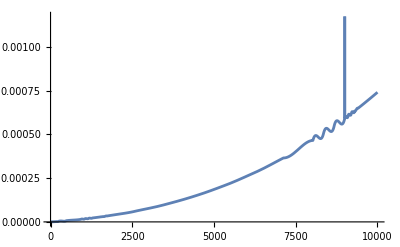

```mathematica
Plot[(-1/(40000 π r^2)InterpolatingFunction[…][r]+1/(40000 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r]),{r,0,10000}]
```

```mathematica
(*Below is taking ρ dp/dρ*)
```

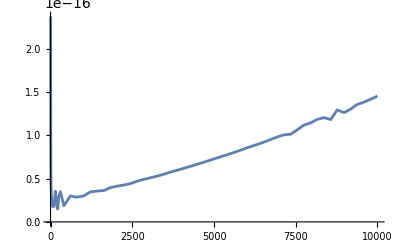

```mathematica
Plot[(mp3[r]/(4 π r^2)) ((-1/(40000 π r^2)InterpolatingFunction[…][r]+1/(40000 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r])),{r,0,10000}]
```

## Combined Plots

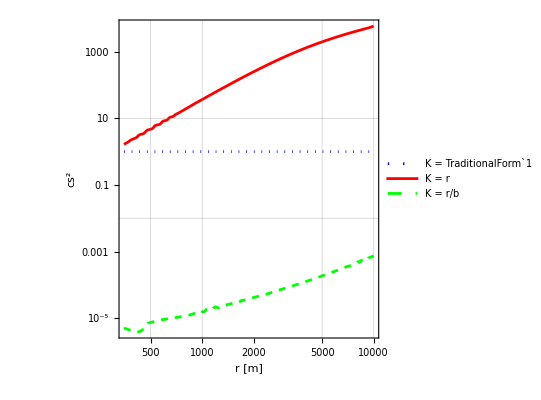

```mathematica
cs2dens=LogLogPlot[{1,((-1/(4 π r^2)InterpolatingFunction[…][r]+1/(4 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r])),(-1/(40000 π r^2)InterpolatingFunction[…][r]+1/(40000 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r])},{r,350,10000},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain], "cs^2"},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = TraditionalForm`1","K = r","K = r/b"},{Left,Top}],GridLines->Automatic,AspectRatio->1,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
Export["cs2dens.pdf",cs2dens]
```

cs2dens.pdf

```mathematica
bulkmodDenas=LogLogPlot[{mp1[r]/(4 π r^2) ,mp2[r]/(4 π r^2)((-1/(4 π r^2)InterpolatingFunction[…][r]+1/(4 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r])) ,mp3[r]/(4 π r^2) ((-1/(40000 π r^2)InterpolatingFunction[…][r]+1/(40000 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r]))},{r,300,10000},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain], "B" Style["[m^-2]",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = TraditionalForm`1","K = r","K = r"},{Above,Center}],GridLines->Automatic,AspectRatio->1,FrameTicks->{{All,None},{All,None}}]
```

-Graphics-

```mathematica
Export["bulkmodDenas.pdf",bulkmodDenas]
```

bulkmodDenas.pdf

## Using Gamma Profiles

## K = 1 and ρ = ρ_0(1-r/b)

```mathematica
(*Finding dρ/dr*)
```

```mathematica
D[Subscript[ρ, 0] (1-r/b),r]
```

-ρ_0/b

```mathematica
(*Finding dp/dr*)
```

```mathematica
gd2=NDSolveValue[{(16^Γ[r] π^(1+2 Γ[r]) (b-r)^2 r (-4 b+3 r) Subscript[ρ, 0]^2+b^2 (((b-r) Subscript[ρ, 0])/b)^Γ[r] (16^Γ[r] π^(2 Γ[r]) (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (r (Λ+12 π (((b-r) Subscript[ρ, 0])/b)^Γ[r])+(3+r^2 Λ) Log[((b-r) Subscript[ρ, 0])/b] Γ'[r]))+16^Γ[r] b π^(2 Γ[r]) r Subscript[ρ, 0] (-(b-r)^2 Λ+π (((b-r) Subscript[ρ, 0])/b)^Γ[r] (-((16 b-15 r) (b-r))+2 r (-4 b+3 r) (Γ[r]+(-b+r) Log[((b-r) Subscript[ρ, 0])/b] Γ'[r]))))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
D[(Subscript[ρ, 0] (1-r/b))^gd2[r],r]
```

((1-r/b) ρ_0)^(InterpolatingFunction[…][r]) (-(InterpolatingFunction[…][r])/(b (1-r/b))+Log[(1-r/b) ρ_0] InterpolatingFunction[…][r])

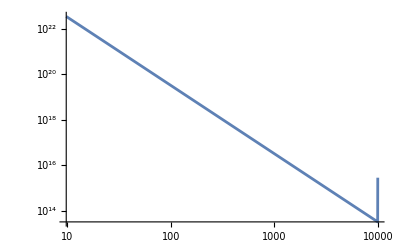

```mathematica
LogLogPlot[(((1-r/b) Subscript[ρ, 0])^(InterpolatingFunction[…][r]) (-1/(b (1-r/b))InterpolatingFunction[…][r]+Log[(1-r/b) Subscript[ρ, 0]] InterpolatingFunction[…][r]))/(-Subscript[ρ, 0]/b)/.{Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

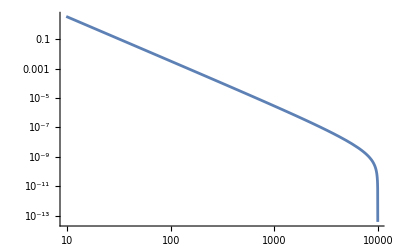

```mathematica
LogLogPlot[(1-r/b) Subscript[ρ, 0](((1-r/b) Subscript[ρ, 0])^(InterpolatingFunction[…][r]) (-1/(b (1-r/b))InterpolatingFunction[…][r]+Log[(1-r/b) Subscript[ρ, 0]] InterpolatingFunction[…][r]))/(-Subscript[ρ, 0]/b)/.{Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## K = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
D[Subscript[ρ, 0] (1-r^2/b^2),r]
```

-(2 r ρ_0)/b^2

```mathematica
gd3=NDSolveValue[{((4 π)^(1+2 Γ[r]) r (b^2-r^2)^2 (-5 b^2+3 r^2) Subscript[ρ, 0]^2+16^Γ[r] b^2 π^(2 Γ[r]) r Subscript[ρ, 0] (-5 (b^2-r^2)^2 Λ+8 π ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r] (-10 b^4+19 b^2 r^2-9 r^4+(-10 b^2 r^2+6 r^4) Γ[r]+r (5 b^4-8 b^2 r^2+3 r^4) Log[(1-r^2/b^2) Subscript[ρ, 0]] Γ'[r]))+5 b^4 ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r] (2^(1+4 Γ[r]) π^(2 Γ[r]) r (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (b+r) (r (Λ+12 π ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r])+(3+r^2 Λ) Log[(1-r^2/b^2) Subscript[ρ, 0]] Γ'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
D[(Subscript[ρ, 0] (1-r^2/b^2))^gd3[r],r]
```

((1-r^2/b^2) ρ_0)^(InterpolatingFunction[…][r]) (-(2 r InterpolatingFunction[…][r])/(b^2 (1-r^2/b^2))+Log[(1-r^2/b^2) ρ_0] InterpolatingFunction[…][r])

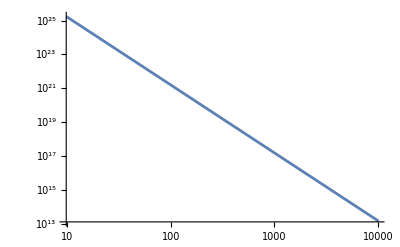

```mathematica
LogLogPlot[(((1-r^2/b^2) Subscript[ρ, 0])^(InterpolatingFunction[…][r]) (-1/(b^2 (1-r^2/b^2))2 r InterpolatingFunction[…][r]+Log[(1-r^2/b^2) Subscript[ρ, 0]] InterpolatingFunction[…][r]))/(-(2 r Subscript[ρ, 0])/b^2)/.{ Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

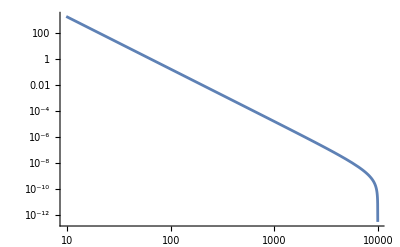

```mathematica
LogLogPlot[(1-r^2/b^2) Subscript[ρ, 0](((1-r^2/b^2) Subscript[ρ, 0])^(InterpolatingFunction[…][r]) (-1/(b^2 (1-r^2/b^2))2 r InterpolatingFunction[…][r]+Log[(1-r^2/b^2) Subscript[ρ, 0]] InterpolatingFunction[…][r]))/(-(2 r Subscript[ρ, 0])/b^2)/.{ Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## Combined Plots

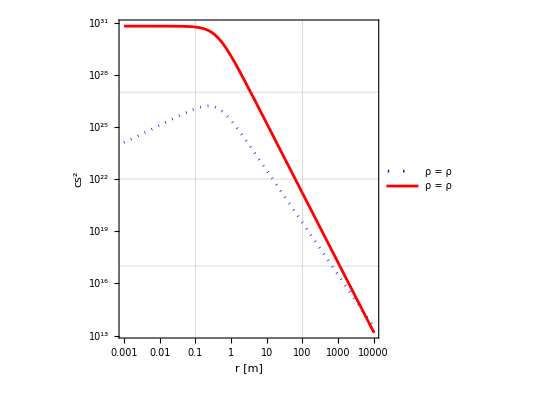

```mathematica
cs2gamma=LogLogPlot[{(((1-r/b) Subscript[ρ, 0])^(InterpolatingFunction[…][r]) (-1/(b (1-r/b))InterpolatingFunction[…][r]+Log[(1-r/b) Subscript[ρ, 0]] InterpolatingFunction[…][r]))/(-Subscript[ρ, 0]/b)/.{ Subscript[ρ, 0]->10^-22,b->10000},(((1-r^2/b^2) Subscript[ρ, 0])^(InterpolatingFunction[…][r]) (-1/(b^2 (1-r^2/b^2))2 r InterpolatingFunction[…][r]+Log[(1-r^2/b^2) Subscript[ρ, 0]] InterpolatingFunction[…][r]))/(-(2 r Subscript[ρ, 0])/b^2)/.{ Subscript[ρ, 0]->10^-22,b->10000}},{r,0.001,9999},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain], "cs^2"},PlotStyle->{{Blue,Dotted},{Red}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ"},{Right,Top}],GridLines->Automatic,AspectRatio->1,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
Export["cs2gamma.pdf",cs2gamma]
```

cs2gamma.pdf

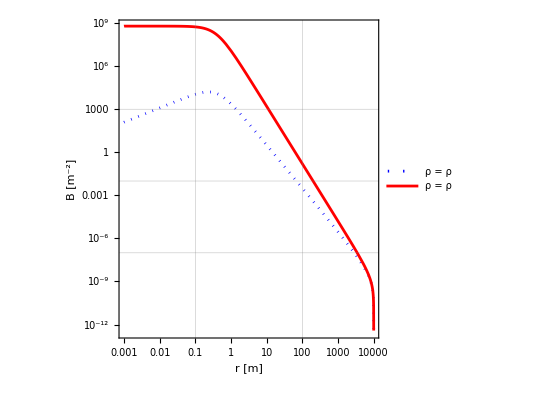

```mathematica
bulkmodGamas=LogLogPlot[{(1-r/b) Subscript[ρ, 0](((1-r/b) Subscript[ρ, 0])^(InterpolatingFunction[…][r]) (-1/(b (1-r/b))InterpolatingFunction[…][r]+Log[(1-r/b) Subscript[ρ, 0]] InterpolatingFunction[…][r]))/(-Subscript[ρ, 0]/b)/.{ Subscript[ρ, 0]->10^-22,b->10000},(1-r^2/b^2) Subscript[ρ, 0](((1-r^2/b^2) Subscript[ρ, 0])^(InterpolatingFunction[…][r]) (-1/(b^2 (1-r^2/b^2))2 r InterpolatingFunction[…][r]+Log[(1-r^2/b^2) Subscript[ρ, 0]] InterpolatingFunction[…][r]))/(-(2 r Subscript[ρ, 0])/b^2)/.{ Subscript[ρ, 0]->10^-22,b->10000}},{r,0.001,9999},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain], "B"Style["[m^-2]",Plain]},PlotStyle->{{Blue,Dotted},{Red}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ"},{Right,Top}],GridLines->Automatic,AspectRatio->1,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
Export["bulkmodGamas.pdf",bulkmodGamas]
```

bulkmodGamas.pdf

## Using K Profiles

## Γ = 1 and ρ = ρ_0(1-r/b)

```mathematica
kd2=NDSolveValue[{(-12 π (b-r)^2 r K[r]^2 Subscript[ρ, 0]+K[r] (b (3-(b-2 r) r Λ)+π r (-16 b^2+23 b r-9 r^2) Subscript[ρ, 0])+(b-r) (-b r Λ-b (3+r^2 Λ) K'[r]+π (4 b-3 r) r Subscript[ρ, 0] (-1+2 r K'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},K[0.001]==0.0001},K,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
D[Subscript[ρ, 0] (1-r/b) kd2[r] ,r]
```

-(ρ_0 InterpolatingFunction[…][r])/b+(1-r/b) ρ_0 InterpolatingFunction[…][r]

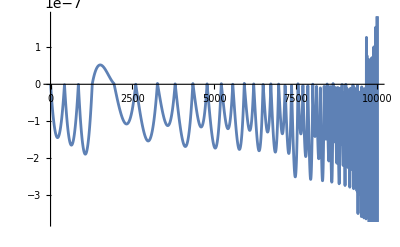

```mathematica
Plot[(-(Subscript[ρ, 0] InterpolatingFunction[…][r])/b+(1-r/b) Subscript[ρ, 0] InterpolatingFunction[…][r])/(-Subscript[ρ, 0]/b)/.{Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

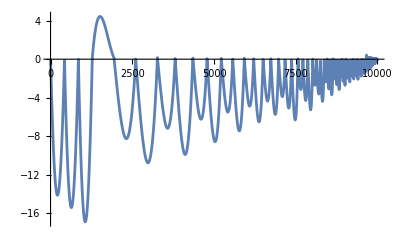

```mathematica
Plot[(Subscript[ρ, 0] (1-r/b)(-(Subscript[ρ, 0] InterpolatingFunction[…][r])/b+(1-r/b) Subscript[ρ, 0] InterpolatingFunction[…][r])/(-Subscript[ρ, 0]/b))10^30/.{Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## Γ = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
kd3=NDSolveValue[{(-60 π r (b^2-r^2)^2 K[r]^2 Subscript[ρ, 0]+r K[r] (5 b^2 (6-b^2 Λ+3 r^2 Λ)-8 π (10 b^4-9 b^2 r^2+3 r^4) Subscript[ρ, 0])-(b-r) (b+r) (4 π r (-5 b^2+3 r^2) Subscript[ρ, 0] (-1+2 r K'[r])+5 b^2 (r Λ+(3+r^2 Λ) K'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},K[0.001]==0.0001},K,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
D[Subscript[ρ, 0] (1-r^2/b^2) kd3[r] ,r]
```

-(2 r ρ_0 InterpolatingFunction[…][r])/b^2+(1-r^2/b^2) ρ_0 InterpolatingFunction[…][r]

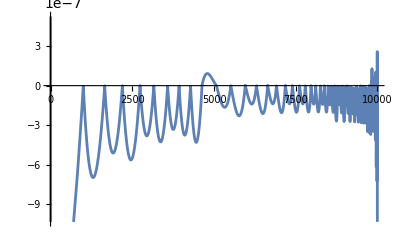

```mathematica
Plot[(-(2 r Subscript[ρ, 0] InterpolatingFunction[…][r])/b^2+(1-r^2/b^2) Subscript[ρ, 0] InterpolatingFunction[…][r])/(-(2 r Subscript[ρ, 0])/b^2)/.{Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

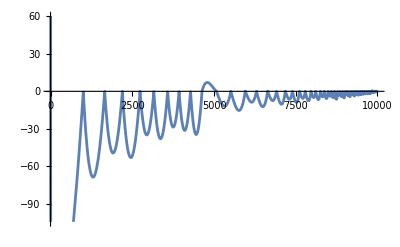

```mathematica
Plot[((1-r^2/b^2) Subscript[ρ, 0] (-(2 r Subscript[ρ, 0] InterpolatingFunction[…][r])/b^2+(1-r^2/b^2) Subscript[ρ, 0] InterpolatingFunction[…][r])/(-(2 r Subscript[ρ, 0])/b^2))10^30/.{Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## Combined Plots

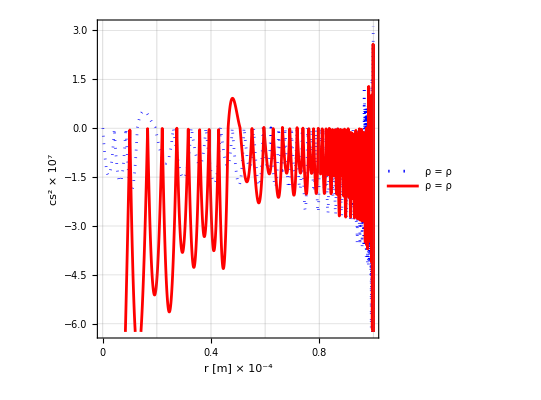

```mathematica
cs2K=Plot[{((-(Subscript[ρ, 0] InterpolatingFunction[…][r])/b+(1-r/b) Subscript[ρ, 0] InterpolatingFunction[…][r])/(-Subscript[ρ, 0]/b))10^7/.{Subscript[ρ, 0]->10^-22,b->10000},((-(2 r Subscript[ρ, 0] InterpolatingFunction[…][r])/b^2+(1-r^2/b^2) Subscript[ρ, 0] InterpolatingFunction[…][r])/(-(2 r Subscript[ρ, 0])/b^2))10^7/.{Subscript[ρ, 0]->10^-22,b->10000},},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain] Style["× 10^-4",Plain], "cs^2"   Style["× 10^7",Plain]},PlotStyle->{{Blue,Dotted},{Red}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ"},{Right,Bottom}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["cs2K.pdf",cs2K]
```

cs2K.pdf

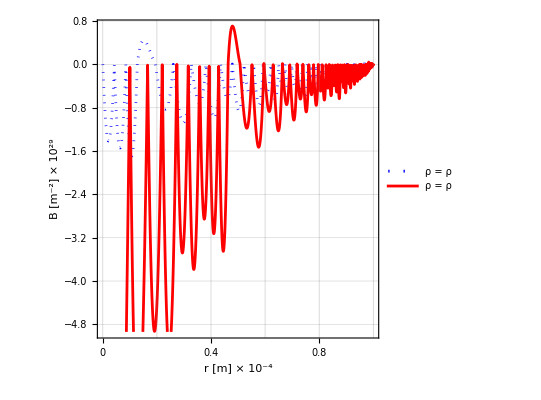

```mathematica
bulkmodKas=Plot[{(1-r/b) Subscript[ρ, 0]((-(Subscript[ρ, 0] InterpolatingFunction[…][r])/b+(1-r/b) Subscript[ρ, 0] InterpolatingFunction[…][r])/(-Subscript[ρ, 0]/b))10^29/.{Subscript[ρ, 0]->10^-22,b->10000},(1-r^2/b^2) Subscript[ρ, 0] ((-(2 r Subscript[ρ, 0] InterpolatingFunction[…][r])/b^2+(1-r^2/b^2) Subscript[ρ, 0] InterpolatingFunction[…][r])/(-(2 r Subscript[ρ, 0])/b^2))10^29/.{Subscript[ρ, 0]->10^-22,b->10000},},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain] Style["× 10^-4",Plain], "B"   Style["[m^-2]",Plain] Style["× 10^29",Plain]},PlotStyle->{{Blue,Dotted},{Red}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ"},{Right,Bottom}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["bulkmodKas.pdf",bulkmodKas]
```

bulkmodKas.pdf

# Null Geodesic

## Mass

## Γ = 1 and K = 1

```mathematica
(*First we assume the conditions for mass, K and Γ. For this case I assumed that K and Γ were both equal to 1. Our goal is to find the conditions for null geodesics(probably not correct wording), this is done by using the Φ' equation. Below we stored each differential order of m[r] needed to solve the Φ' equation.*)
```

```mathematica
m1=NDSolveValue[{-16 π^2 m'[r] (6 (3 m[r]+r (-1+m'[r])) m'[r]+r (3 r+r^3 Λ-6 m[r]) m''[r])==0/.Λ->10^-52,m[0.001]==10^-5,m[9000]==0.1},m,{r,0.0001,10000}]
```

InterpolatingFunction[…]

```mathematica
mp1=NDSolveValue[{-16 π^2 m'[r] (6 (3 m[r]+r (-1+m'[r])) m'[r]+r (3 r+r^3 Λ-6 m[r]) m''[r])==0/.Λ->10^-52,m[0.001]==10^-5,m[9000]==0.1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

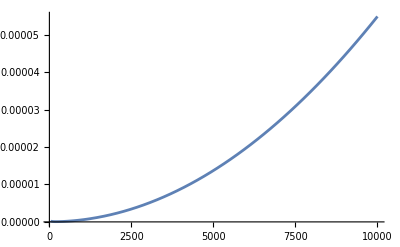

```mathematica
Plot[r((12 π r^3 (K[r] (m'[r]/(4 π r^2))^Γ[r])+3 m[r]+ Λ r^3)/(r (3 r-6 m[r]+Λ r^3)))/.{Γ'[r]->0,Γ[r]->1,K'[r]->0,K[r]->1,m[r]->m1[r],m'[r]->mp1[r],Λ->10^-52},{r,35,10000}]
```

## Γ = 1 and K = r

```mathematica
mkr=NDSolveValue[{-16 π^2 m'[r] ((r^2 (-3+r Λ)+(3+9 r) m[r]) m'[r]+3 r^2 (1+r) m'[r]^2+r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52},m[0.001]==10^-5,m[9000]==1},m,{r,0.0001,9000}]
```

InterpolatingFunction[…]

```mathematica
mkrp=NDSolveValue[{-16 π^2 m'[r] ((r^2 (-3+r Λ)+(3+9 r) m[r]) m'[r]+3 r^2 (1+r) m'[r]^2+r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52},m[0.001]==10^-5,m[9000]==1},m',{r,0.0001,9000}]
```

InterpolatingFunction[…]

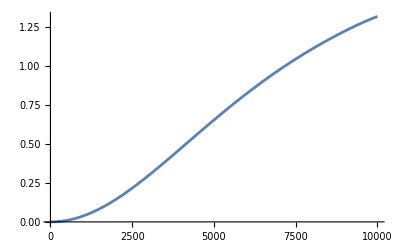

```mathematica
Plot[r((12 π r^3 (K[r] (m'[r]/(4 π r^2))^Γ[r])+3 m[r]+ Λ r^3)/(r (3 r-6 m[r]+Λ r^3)))/.{Γ[r]->1,m[r]->mkr[r],m'[r]->mkrp[r],Λ->10^-52,K[r]->r},{r,3,10000}]
```

## Γ = 1 and K = r/b

```mathematica
m3=NDSolveValue[{-1/b^2 16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52,b->10000},m[0.001]==0,m[9000]==1},m,{r,0.0001,10000}]
```

InterpolatingFunction[…]

```mathematica
mp3=NDSolveValue[{-1/b^2 16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52,b->10000},m[0.001]==0,m[9000]==1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

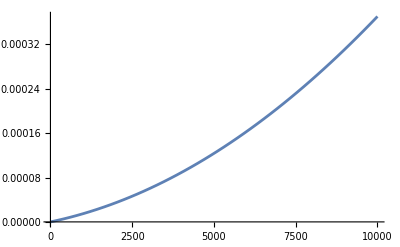

```mathematica
Plot[r((12 π r^3 (K[r] (m'[r]/(4 π r^2))^Γ[r])+3 m[r]+ Λ r^3)/(r (3 r-6 m[r]+Λ r^3)))/.{Γ[r]->1,m[r]->m3[r],m'[r]->mp3[r],Λ->10^-52,K[r]->r/10000},{r,3,10000}]
```

## Combined

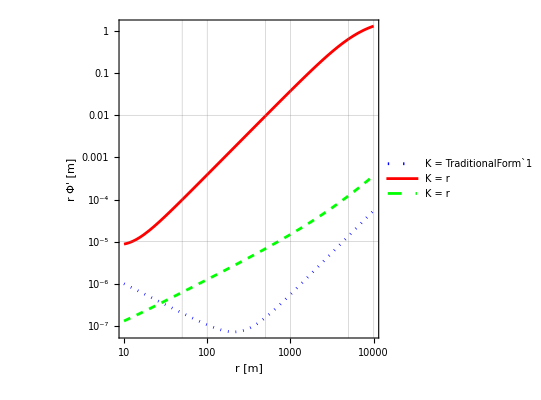

```mathematica
nulgeoKas=LogLogPlot[{r((12 π r^3 ( (mp1[r]/(4 π r^2)))+3 m1[r]+ Λ r^3)/(r (3 r-6 m1[r]+Λ r^3)))/.Λ->10^-52,r((12 π r^3 (r (mkrp[r]/(4 π r^2)))+3 mkr[r]+ Λ r^3)/(r (3 r-6 mkr[r]+Λ r^3)))/.Λ->10^-52 ,r((12 π r^3 (r/10000 (mp3[r]/(4 π r^2)))+3 m3[r]+ Λ r^3)/(r (3 r-6 m3[r]+Λ r^3)))/.Λ->10^-52 },{r,10,10000},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain], "r Φ'" Style["[m]",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = TraditionalForm`1","K = r","K = r"},{Left,Top}],GridLines->Automatic,AspectRatio->1,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
Export["nulgeoKas.pdf",nulgeoKas]
```

nulgeoKas.pdf

## K

## Γ = 1 and ρ = ρ_0

```mathematica
Integrate[4 π r^2 Subscript[ρ, 0] ,r]
```

4/3 π r^3 ρ_0

```mathematica
FullSimplify[4 π r^2 Subscript[ρ, 0] ]
```

4 π r^2 ρ_0

```mathematica
kd1=NDSolveValue[{(-r (1+K[r]) (Λ+4 (π+3 π K[r]) Subscript[ρ, 0])-(3+r^2 Λ-8 π r^2 Subscript[ρ, 0]) K'[r])==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22},K[0.001]==0.0001},K,{r,0.001,10000}]
```

InterpolatingFunction[…]

```mathematica
FullSimplify[r((12 π r^3 (K[r] (m'[r]/(4 π r^2))^Γ[r])+3 m[r]+ Λ r^3)/(r (3 r-6 m[r]+Λ r^3)))/.{Γ[r]->1,m'[r]->4 π r^2 Subscript[ρ, 0],m[r]->4/3 π r^3 Subscript[ρ, 0],K[r]->kd1[r]}]
```

(r^2 (Λ+4 ρ_0 (π+3 π InterpolatingFunction[…][r])))/(3+r^2 Λ-8 π r^2 ρ_0)

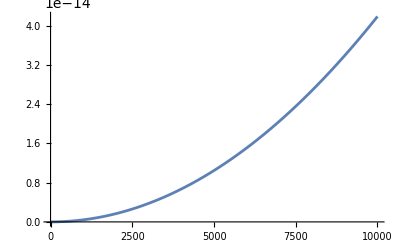

```mathematica
Plot[(r^2 (Λ+4 Subscript[ρ, 0] (π+3 π InterpolatingFunction[…][r])))/(3+r^2 Λ-8 π r^2 Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## Γ = 1 and ρ = ρ_0(1-r/b)

```mathematica
(*We can also assume a density distribution and solve Φ'. This is done by using the relationship ρ = m'[r]/(4 πr^2)*)
```

```mathematica
(*m[r] is below*)
```

```mathematica
Integrate[4 π r^2 Subscript[ρ, 0] (1-r/b),r]
```

4 π (r^3/3-r^4/(4 b)) ρ_0

```mathematica
(*m'[r] is below*)
```

```mathematica
FullSimplify[4 π r^2 Subscript[ρ, 0] (1-r/b)]
```

4 π r^2 (1-r/b) ρ_0

```mathematica
kd2=NDSolveValue[{(-12 π (b-r)^2 r K[r]^2 Subscript[ρ, 0]+K[r] (b (3-(b-2 r) r Λ)+π r (-16 b^2+23 b r-9 r^2) Subscript[ρ, 0])+(b-r) (-b r Λ-b (3+r^2 Λ) K'[r]+π (4 b-3 r) r Subscript[ρ, 0] (-1+2 r K'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},K[0.001]==0.0001},K,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
FullSimplify[r((12 π r^3 (K[r] (m'[r]/(4 π r^2))^Γ[r])+3 m[r]+ Λ r^3)/(r (3 r-6 m[r]+Λ r^3)))/.{Γ[r]->1,m'[r]->4 π r^2 (1-r/b) Subscript[ρ, 0],m[r]->4 π (r^3/3-r^4/(4 b)) Subscript[ρ, 0],K[r]->kd2[r]}]
```

(r^2 (b Λ+π ρ_0 (4 b-3 r+12 (b-r) InterpolatingFunction[…][r])))/(b (3+r^2 Λ)+2 π r^2 (-4 b+3 r) ρ_0)

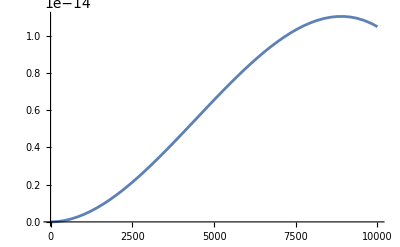

```mathematica
Plot[(r^2 (b Λ+π Subscript[ρ, 0] (4 b-3 r+12 (b-r) InterpolatingFunction[…][r])))/(b (3+r^2 Λ)+2 π r^2 (-4 b+3 r) Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## Γ = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
Integrate[4 π r^2 Subscript[ρ, 0] (1-r^2/b^2),r]
```

4 π (r^3/3-r^5/(5 b^2)) ρ_0

```mathematica
FullSimplify[4 π r^2 Subscript[ρ, 0] (1-r^2/b^2)]
```

4 π r^2 (1-r^2/b^2) ρ_0

```mathematica
kd3=NDSolveValue[{(-60 π r (b^2-r^2)^2 K[r]^2 Subscript[ρ, 0]+r K[r] (5 b^2 (6-b^2 Λ+3 r^2 Λ)-8 π (10 b^4-9 b^2 r^2+3 r^4) Subscript[ρ, 0])-(b-r) (b+r) (4 π r (-5 b^2+3 r^2) Subscript[ρ, 0] (-1+2 r K'[r])+5 b^2 (r Λ+(3+r^2 Λ) K'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},K[0.001]==0.0001},K,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
FullSimplify[r((12 π r^3 (K[r] (m'[r]/(4 π r^2))^Γ[r])+3 m[r]+ Λ r^3)/(r (3 r-6 m[r]+Λ r^3)))/.{Γ[r]->1,m'[r]->4 π r^2 (1-r^2/b^2) Subscript[ρ, 0],m[r]->4 π (r^3/3-r^5/(5 b^2)) Subscript[ρ, 0],K[r]->kd3[r]}]
```

(r^2 (5 b^2 Λ+4 π ρ_0 (5 b^2-3 r^2+15 (b-r) (b+r) InterpolatingFunction[…][r])))/(5 b^2 (3+r^2 Λ)+8 π r^2 (-5 b^2+3 r^2) ρ_0)

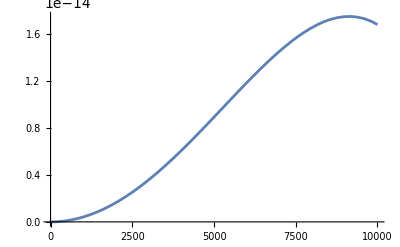

```mathematica
Plot[(r^2 (5 b^2 Λ+4 π Subscript[ρ, 0] (5 b^2-3 r^2+15 (b-r) (b+r) InterpolatingFunction[…][r])))/(5 b^2 (3+r^2 Λ)+8 π r^2 (-5 b^2+3 r^2) Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## Combined

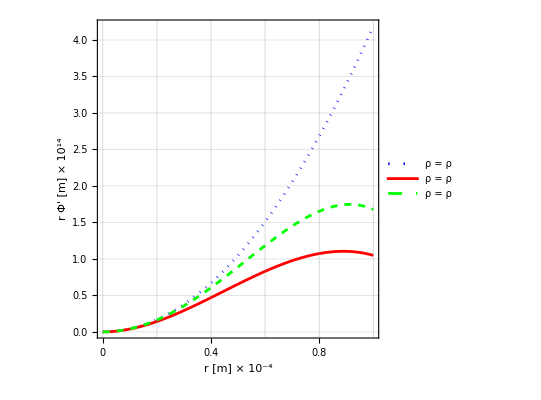

```mathematica
nulgeoRhoas=Plot[{(r^2 (Λ+4 Subscript[ρ, 0] (π+3 π InterpolatingFunction[…][r])))/(3+r^2 Λ-8 π r^2 Subscript[ρ, 0]) (10^14)/.{Λ->10^-52,Subscript[ρ, 0]->10^-22},(r^2 (b Λ+π Subscript[ρ, 0] (4 b-3 r+12 (b-r) InterpolatingFunction[…][r])))/(b (3+r^2 Λ)+2 π r^2 (-4 b+3 r) Subscript[ρ, 0]) (10^14)/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},(r^2 (5 b^2 Λ+4 π Subscript[ρ, 0] (5 b^2-3 r^2+15 (b-r) (b+r) InterpolatingFunction[…][r])))/(5 b^2 (3+r^2 Λ)+8 π r^2 (-5 b^2+3 r^2) Subscript[ρ, 0]) (10^14)/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000}},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain] Style["× 10^-4",Plain], "r Φ'" Style["[m]",Plain] Style["× 10^14",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["nulgeoRhoas.pdf",nulgeoRhoas]
```

nulgeoRhoas.pdf

## Γ

## K = 1 and ρ = ρ_0

```mathematica
Integrate[4 π r^2 Subscript[ρ, 0] ,r]
```

4/3 π r^3 ρ_0

```mathematica
FullSimplify[4 π r^2 Subscript[ρ, 0] ]
```

4 π r^2 ρ_0

```mathematica
gd1=NDSolveValue[{(3 (4 π)^(1+2 Γ[r]) r Subscript[ρ, 0]^(2 Γ[r])+r Subscript[ρ, 0] (16^Γ[r] π^(2 Γ[r]) Λ+(4 π)^(1+2 Γ[r]) Subscript[ρ, 0])+16^Γ[r] π^(2 Γ[r]) Subscript[ρ, 0]^Γ[r] (r (Λ+16 π Subscript[ρ, 0])+Log[Subscript[ρ, 0]] (3+r^2 Λ-8 π r^2 Subscript[ρ, 0]) Γ'[r]))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

InterpolatingFunction[…]

```mathematica
FullSimplify[r((12 π r^3 (K[r] (m'[r]/(4 π r^2))^Γ[r])+3 m[r]+ Λ r^3)/(r (3 r-6 m[r]+Λ r^3)))/.{Γ[r]->gd1[r],m'[r]->4 π r^2 Subscript[ρ, 0],m[r]->4/3 π r^3 Subscript[ρ, 0],K[r]->1}]
```

(r^2 (Λ+4 π (ρ_0+3 ρ_0^(InterpolatingFunction[…][r]))))/(3+r^2 Λ-8 π r^2 ρ_0)

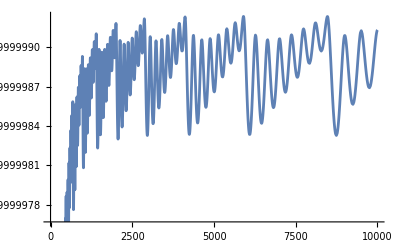

```mathematica
Plot[(r^2 (Λ+4 π (Subscript[ρ, 0]+3 Subscript[ρ, 0]^(InterpolatingFunction[…][r]))))/(3+r^2 Λ-8 π r^2 Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## K = 1 and ρ = ρ_0(1-r/b)

```mathematica
gd2=NDSolveValue[{(16^Γ[r] π^(1+2 Γ[r]) (b-r)^2 r (-4 b+3 r) Subscript[ρ, 0]^2+b^2 (((b-r) Subscript[ρ, 0])/b)^Γ[r] (16^Γ[r] π^(2 Γ[r]) (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (r (Λ+12 π (((b-r) Subscript[ρ, 0])/b)^Γ[r])+(3+r^2 Λ) Log[((b-r) Subscript[ρ, 0])/b] Γ'[r]))+16^Γ[r] b π^(2 Γ[r]) r Subscript[ρ, 0] (-(b-r)^2 Λ+π (((b-r) Subscript[ρ, 0])/b)^Γ[r] (-((16 b-15 r) (b-r))+2 r (-4 b+3 r) (Γ[r]+(-b+r) Log[((b-r) Subscript[ρ, 0])/b] Γ'[r]))))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
FullSimplify[r((12 π r^3 (K[r] (m'[r]/(4 π r^2))^Γ[r])+3 m[r]+ Λ r^3)/(r (3 r-6 m[r]+Λ r^3)))/.{Γ[r]->gd2[r],m'[r]->4 π r^2 (1-r/b) Subscript[ρ, 0],m[r]->4 π (r^3/3-r^4/(4 b)) Subscript[ρ, 0],K[r]->1}]
```

(r^2 (π (4 b-3 r) ρ_0+b (Λ+12 π (((b-r) ρ_0)/b)^(InterpolatingFunction[…][r]))))/(b (3+r^2 Λ)+2 π r^2 (-4 b+3 r) ρ_0)

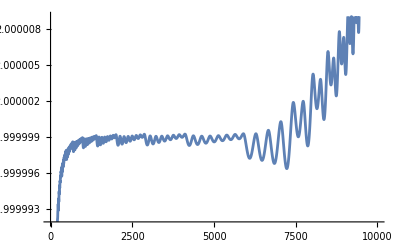

```mathematica
Plot[(r^2 (π (4 b-3 r) Subscript[ρ, 0]+b (Λ+12 π (((b-r) Subscript[ρ, 0])/b)^(InterpolatingFunction[…][r]))))/(b (3+r^2 Λ)+2 π r^2 (-4 b+3 r) Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## K = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
gd3=NDSolveValue[{((4 π)^(1+2 Γ[r]) r (b^2-r^2)^2 (-5 b^2+3 r^2) Subscript[ρ, 0]^2+16^Γ[r] b^2 π^(2 Γ[r]) r Subscript[ρ, 0] (-5 (b^2-r^2)^2 Λ+8 π ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r] (-10 b^4+19 b^2 r^2-9 r^4+(-10 b^2 r^2+6 r^4) Γ[r]+r (5 b^4-8 b^2 r^2+3 r^4) Log[(1-r^2/b^2) Subscript[ρ, 0]] Γ'[r]))+5 b^4 ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r] (2^(1+4 Γ[r]) π^(2 Γ[r]) r (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (b+r) (r (Λ+12 π ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r])+(3+r^2 Λ) Log[(1-r^2/b^2) Subscript[ρ, 0]] Γ'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
FullSimplify[r((12 π r^3 (K[r] (m'[r]/(4 π r^2))^Γ[r])+3 m[r]+ Λ r^3)/(r (3 r-6 m[r]+Λ r^3)))/.{Γ[r]->gd3[r],m'[r]->4 π r^2 (1-r^2/b^2) Subscript[ρ, 0],m[r]->4 π (r^3/3-r^5/(5 b^2)) Subscript[ρ, 0],K[r]->1}]
```

(r^2 (4 π (5 b^2-3 r^2) ρ_0+5 b^2 (Λ+12 π ((1-r^2/b^2) ρ_0)^(InterpolatingFunction[…][r]))))/(5 b^2 (3+r^2 Λ)+8 π r^2 (-5 b^2+3 r^2) ρ_0)

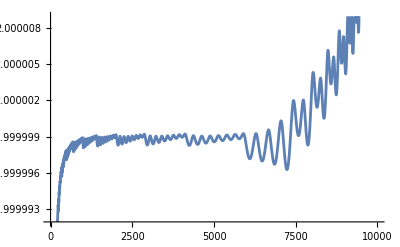

```mathematica
Plot[(r^2 (4 π (5 b^2-3 r^2) Subscript[ρ, 0]+5 b^2 (Λ+12 π ((1-r^2/b^2) Subscript[ρ, 0])^(InterpolatingFunction[…][r]))))/(5 b^2 (3+r^2 Λ)+8 π r^2 (-5 b^2+3 r^2) Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},{r,0,10000}]
```

## Combined

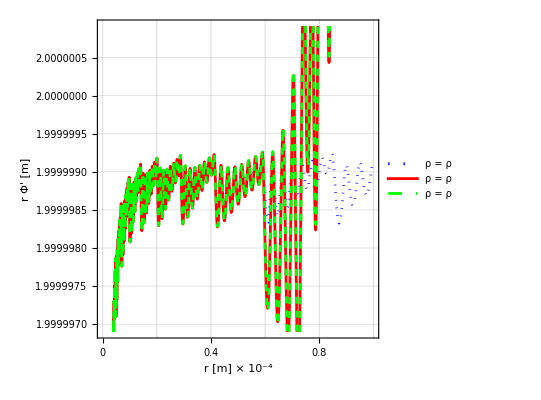

```mathematica
nulgeoGamas=Plot[{(r^2 (Λ+4 π (Subscript[ρ, 0]+3 Subscript[ρ, 0]^(InterpolatingFunction[…][r]))))/(3+r^2 Λ-8 π r^2 Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},(r^2 (π (4 b-3 r) Subscript[ρ, 0]+b (Λ+12 π (((b-r) Subscript[ρ, 0])/b)^(InterpolatingFunction[…][r]))))/(b (3+r^2 Λ)+2 π r^2 (-4 b+3 r) Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},(r^2 (4 π (5 b^2-3 r^2) Subscript[ρ, 0]+5 b^2 (Λ+12 π ((1-r^2/b^2) Subscript[ρ, 0])^(InterpolatingFunction[…][r]))))/(5 b^2 (3+r^2 Λ)+8 π r^2 (-5 b^2+3 r^2) Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000}},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain] Style["× 10^-4",Plain], "r Φ'" Style["[m]",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["nulgeoGamas.pdf",nulgeoGamas]
```

nulgeoGamas.pdf

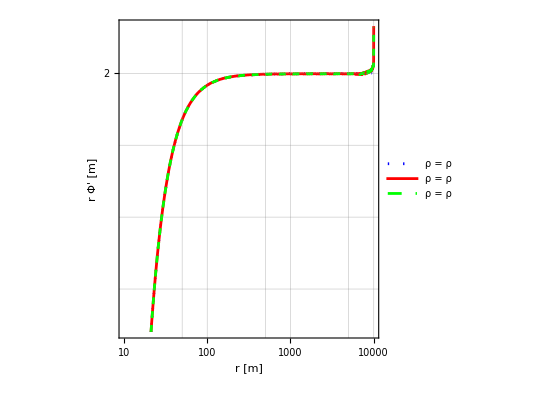

```mathematica
nulgeoGamasLog=LogLogPlot[{(r^2 (Λ+4 π (Subscript[ρ, 0]+3 Subscript[ρ, 0]^(InterpolatingFunction[…][r]))))/(3+r^2 Λ-8 π r^2 Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},(r^2 (π (4 b-3 r) Subscript[ρ, 0]+b (Λ+12 π (((b-r) Subscript[ρ, 0])/b)^(InterpolatingFunction[…][r]))))/(b (3+r^2 Λ)+2 π r^2 (-4 b+3 r) Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000},(r^2 (4 π (5 b^2-3 r^2) Subscript[ρ, 0]+5 b^2 (Λ+12 π ((1-r^2/b^2) Subscript[ρ, 0])^(InterpolatingFunction[…][r]))))/(5 b^2 (3+r^2 Λ)+8 π r^2 (-5 b^2+3 r^2) Subscript[ρ, 0])/.{Λ->10^-52,Subscript[ρ, 0]->10^-22,b->10000} },{r,10,10000},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain], "r Φ'" Style["[m]",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Right,Bottom}],GridLines->Automatic,AspectRatio->1,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
Export["nulgeoGamasLog.pdf",nulgeoGamasLog]
```

nulgeoGamasLog.pdf

$Aborted